```mathematica
(*81 lines per section*)
(*r Zr-Zr C-Zr C-C Total*)
```

## Classifier for Frenkel pairs

```mathematica
Ideas to improve the classifier:
1) Each volume has its own classifier
2) Difference the PDF with respect to an average perfect run at that temperature
3) Include Zr-C as well as C-C PDF
4) Include a few steps a high tempertures in the training model
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/collective_PDFs"];
files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt"};
pdfData=Table[ReadList[files[[i]],{Number,Number,Number,Number,Number}],{i,1,5}];
```

```mathematica
names={"70","129","142","174","1126"};
fullNames={"Bound-dimer","Unbound-dimer","Unbound-trimer","Unbound-trimer","Unbound-tetramer"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer"};
volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};
```

```mathematica
zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,5}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,5}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,5}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,5}];
```

```mathematica
ListLinePlot[Partition[zrzr[[1]],81],PlotRange->All];
ListLinePlot[Partition[zrzr[[3]],81],PlotRange->All];
```

```mathematica
Table[ListLinePlot[Partition[cc[[i]],81],PlotRange->All],{i,1,5}];
```

```mathematica
ListLinePlot[Partition[tot[[1]],81][[1;;10]],PlotRange->All];
```

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

```mathematica
ccAnimation=Table[With[{name=cc},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,PlotLabel->fullNames[[j]],FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,5}]
```

{,,,,}

```mathematica
(*Export["B2-test-data-300K.avi",ccAnimation[[1]],"Animation","AnimationRepetitions"->2,"ControlAppearance"->None]*)
```

```mathematica
plotStyle={PlotRange->{{0,5},{0,.5}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTrainingCC=Table[With[{name=cc},Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[fullNames[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,5}];
framesTrainingCCJoined=Join[framesTrainingCC[[1]],framesTrainingCC[[2]]];
Export["framesTrainingCC.gif",framesTrainingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None,"FrameRate"->25]
```

framesTrainingCC.gif

```mathematica
With[{name=zrzr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

ListAnimate[{},15]

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

```mathematica
trainSet=Table[Table[{Partition[cc[[i]],81][[j]]->ToString@fullNames[[i]]},{j,1,2}],{i,1,5}];
```

```mathematica
Options@Classify
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

```mathematica
methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=100,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

1. | 1. | 1. | 1. | 1.
0.862745 | 0.686275 | 0.862745 | 0.862745 | 0.941176
1. | 0.921569 | 0.882353 | 1. | 1.
1. | 1. | 0.941176 | 1. | 0.980392
1. | 0.980392 | 0.921569 | 1. | 0.980392
1. | 1. | 1. | 1. | 1.

```mathematica
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | 
LogisticRegression | 1. | 1. | 1. | 1. | 1.
Markov | 0.843137 | 0.784314 | 0.686275 | 0.784314 | 0.941176
NaiveBayes | 1. | 0.941176 | 1. | 1. | 1.
NearestNeighbors | 1. | 1. | 0.980392 | 1. | 0.980392
RandomForest | 1. | 1. | 0.882353 | 0.980392 | 1.
SupportVectorMachine | 1. | 1. | 1. | 1. | 1.

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/test-data"];
filesTest={"1-Frenkel_500_222kp-6hr-9.602/pdf.70.4801.1_866.txt","2-Frenkel_500_222kp-6hr-9.700/pdf.test.4850.1_1021.txt"};
pdfDataTest=Table[ReadList[filesTest[[i]],{Number,Number,Number,Number,Number}],{i,1,2}];
```

```mathematica
zrzrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[2]]},{i,1,2}];
czrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[3]]},{i,1,2}];
ccTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[4]]},{i,1,2}];
totTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[5]]},{i,1,2}];
```

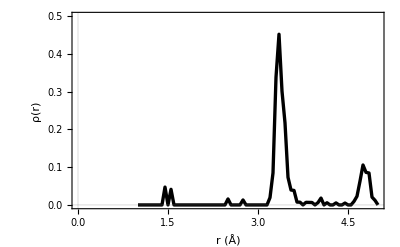

```mathematica
ListLinePlot[Partition[ccTest[[1]],81][[1]],plotStyle]
```

```mathematica
vols
```

vols

```mathematica
ccTestAnimation=Table[With[{name=ccTest},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[volumes[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,2}]
```

{,}

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTestingCC=Table[With[{name=ccTest},Table[ListLinePlot[Partition[name[[j]],81][[i]],Frame->True,plotStyle,PlotLabel->Style["3000 K MD",18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,1}];
framesTestingCCJoined=Join[framesTestingCC[[1]],framesTestingCC[[1]]];
Export["framesTestingCC.gif",framesTestingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None]
```

framesTestingCC.gif

{Null,Null,Null,Null,Null}

```mathematica
DeleteDuplicates[scoresTest]
```

{Null}

```mathematica
c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]]
```

```mathematica
c[Transpose[Partition[ccTest[[1]],81][[2]]][[1]]]
```

Bound-tetramer

```mathematica
Transpose[Partition[ccTest[[1]],81][[1]]][[2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0473,0.,0.0414,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0159,0.,0.,0.,0.,0.0132,0.,0.,0.,0.,0.,0.,0.,0.,0.0194,0.0848,0.338,0.452,0.3012,0.2173,0.0731,0.0395,0.0384,0.0075,0.0073,0.,0.0069,0.0067,0.0065,0.,0.0062,0.0182,0.,0.0058,0.,0.,0.0054,0.,0.,0.005,0.,0.,0.0094,0.023,0.063,0.1058,0.0863,0.0846,0.0207,0.0122,0.}

```mathematica
c[Transpose[Partition[ccTest[[1]],81][[1]]][[1]]]
```

Bound-tetramer

```mathematica
testOut=With[{trainSize=1,valSize=5,maxTypes=2},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Unbound-dimer | Unbound-trimer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer
Unbound-tetramer | Unbound-tetramer

```mathematica
With[{trainSize=2,valSize=150,maxTypes=1},Table[Table[c[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]]
```

{{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer},{Bound-tetramer}}

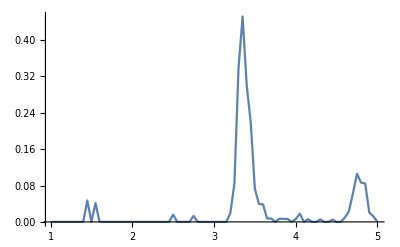

```mathematica
ListLinePlot[{testList},PlotRange->All]
```

```mathematica
train=Table[Partition[cc[[i]],81][[1]],{i,1,5}];
```

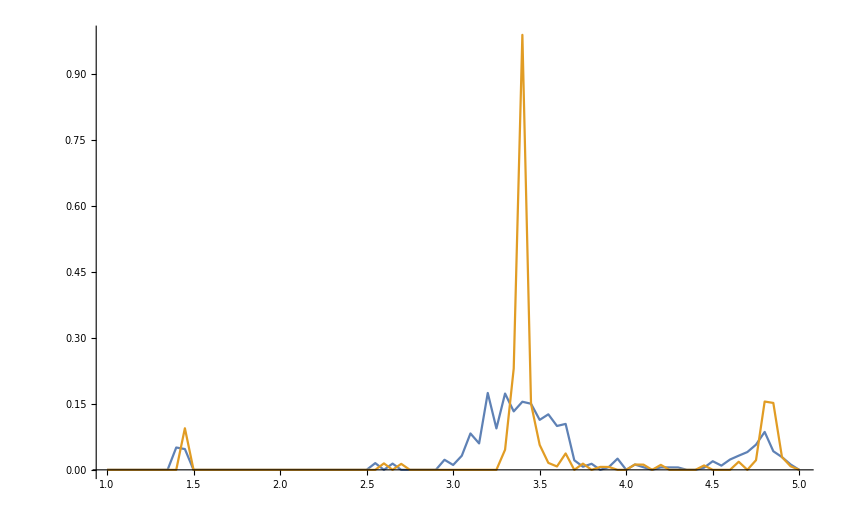

```mathematica
ListLinePlot[{Partition[ccTest[[1]],81][[3]],train[[3]]},PlotRange->All]
```

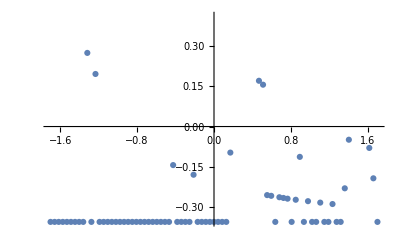

```mathematica
ListPlot@Standardize[testList]
```

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=100,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c2=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c2[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```